# MS-C1650 - Numerical Analysis Week 20: Lecture 9: Numerical Methods for ODEs

## Harri Hakula, 2021

## Setting

To begin, consider an initial value problem for a linear first-order ODE.

This is a linear first-order ODE:

```mathematica
linearequation = y'[t]-3*t*y[t]==1;
```

Notice that the general solution is a linear function of the arbitrary constant Cpaclet:ref/C[1]:

```mathematica
generalsolution = DSolve[linearequation, y[t],t]
```

{{y[t]→ⅇ^((3 t^2)/2) C[1]+ⅇ^((3 t^2)/2) √(π/6) Erf[√(3/2) t]}}

This finds a particular solution for the initial condition y[0]==4:

```mathematica
particularsolution = DSolve[{linearequation, y[0]==4}, y,t]
```

{{y→Function[{t},1/6 ⅇ^((3 t^2)/2) (24+√(6 π) Erf[√(3/2) t])]}}

This verifies that the solution satisfies both the equation and the initial condition:

```mathematica
linearequation/.particularsolution[[1]]
```

True

```mathematica
y[0]/.particularsolution[[1]]
```

4

Here is the solution to the same problem with the general initial condition y[0]==a:

```mathematica
particularsolution = DSolve[{linearequation, y[0]==a}, y,t]
```

{{y→Function[{t},1/6 ⅇ^((3 t^2)/2) (6 a+√(6 π) Erf[√(3/2) t])]}}

This plots several integral curves of the equation for different values of a. The plot shows that the solutions have an inflection point if the parameter a lies between -1 and 1, while a global maximum or minimum arises for other values of a:

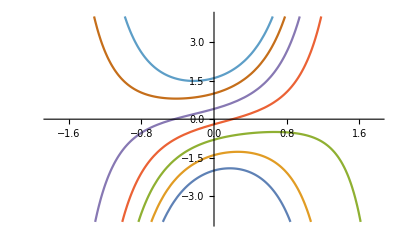

```mathematica
base=Plot[Evaluate[Table[y[t]/.particularsolution[[1]]/.a-> i, {i,-2,2,0.6}]], {t,-1.8,1.8}, PlotRange -> {-4,4}]
```

### Challenge

Any numerical method has to be able to track the particular solution fixed by the initial value.

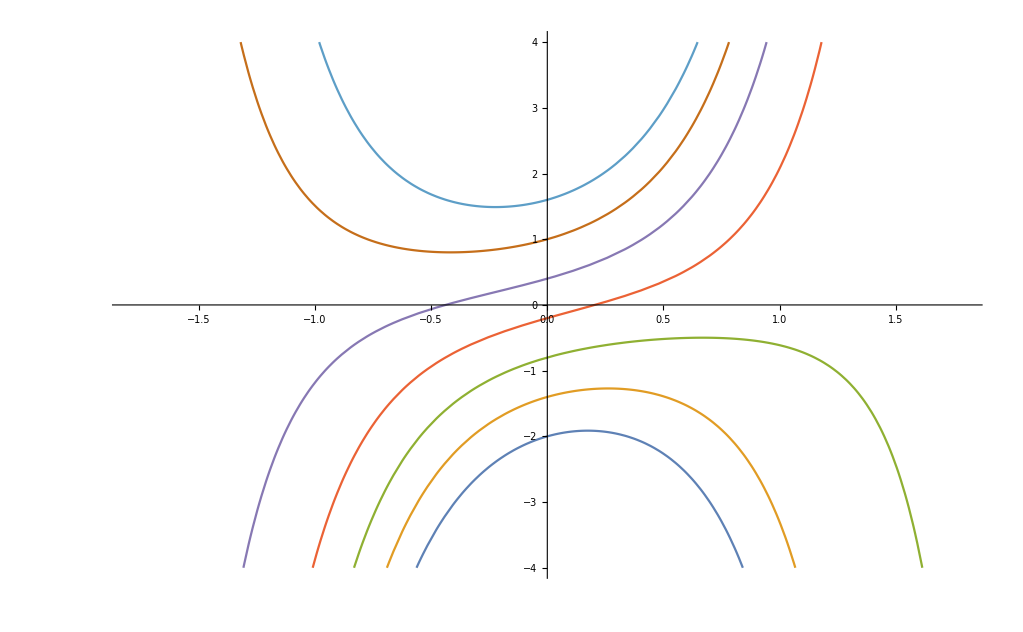

## Detail

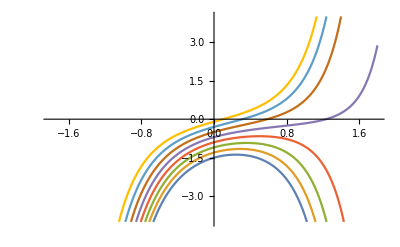

```mathematica
base=Plot[Evaluate[Table[y[t]/.particularsolution[[1]]/.a-> i, {i,-1.5,0,0.2}]], {t,-1.8,1.8}, PlotRange -> {-4,4},ImageSize->Full]
```

## Euler’s Method

```mathematica
h=0.4
```

0.4

```mathematica
f[t_,y_]:=1+3*t*y
```

```mathematica
t0=0;
y0=-0.8;
trajectory={{t0,y0}};
y=y0;
Do[
y=y+h f[(k-1)h,y];
AppendTo[trajectory,{k h,y}],{k,Ceiling[2/h]}];
```

```mathematica
path=ListPlot[trajectory,Joined->True,Axes->False,PlotStyle->{Thick,Black},PlotRange->All];
```

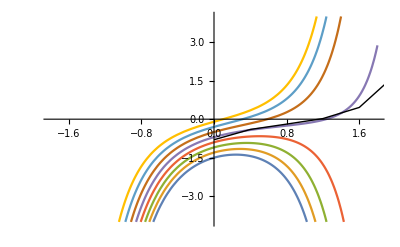

```mathematica
Show[base,path]
```

## Euler’s Method

```mathematica
h=0.02
```

0.02

```mathematica
f[t_,y_]:=1+3*t*y
```

```mathematica
t0=0;
y0=-0.8;
trajectory={{t0,y0}};
y=y0;
Do[
y=y+h f[(k-1)h,y];
AppendTo[trajectory,{k h,y}],{k,Ceiling[2/h]}];
```

```mathematica
path=ListPlot[trajectory,Joined->True,Axes->False,PlotStyle->{Thick,Black},PlotRange->All];
```

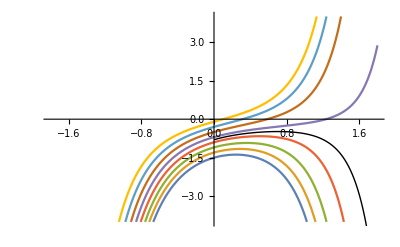

```mathematica
Show[base,path]
```